#### Find wavefunction as a function of axial position

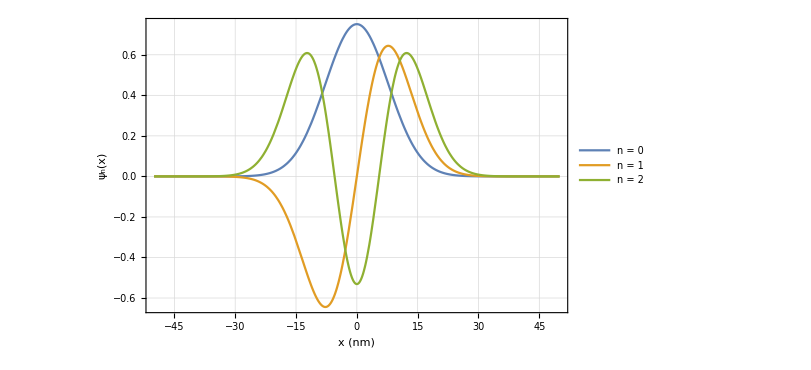

```mathematica
ω=2π(3.0)10^6;(*axial secular frequency*)
m=56 1.66 10^-27;(*mass*)

ℏ=1.055 10^-34;

ψ[n_,x_]:=1/(√(2^n n!))π^(-1/4)Exp[-(x/(√(ℏ/(m ω))))^2/2]HermiteH[n,(x/(√(ℏ/(m ω))))];

nMin=0;
nMax=2;

xMin=-50;(*nm*)
xMax=50;(*nm*)

plotData=Table[ψ[n,10^-9 x],{n,nMin,nMax}];
Plot[plotData,{x,xMin,xMax},PlotRange->All,Frame->True,GridLines->Automatic,FrameLabel->{"x (nm)","ψ_n(x)"},ImageSize->600,FrameStyle->Directive[Black,16],PlotLegends->Placed[Table["n = "<>ToString[n],{n,nMin,nMax}],{0.9,0.85}]]
```

#### Find electric field as a function of axial position

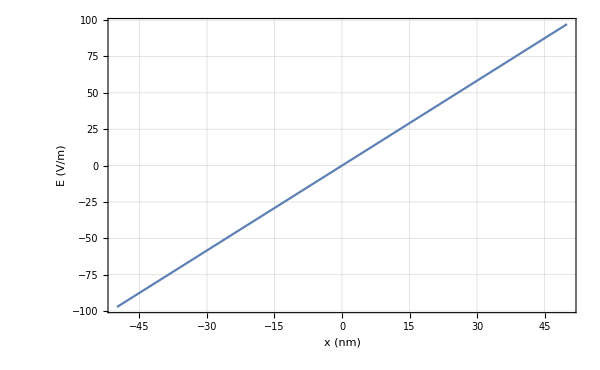

```mathematica
Ω=2π(20)10^6;

e=1.602 10^-19;


(*For +/- V, not for 2 rods grounded*)
(*V/Subscript[r, 0]^2 == mωΩ/(√2 e)*)
Ex=2((m ω Ω)/(√2 e))(10^-9 x);

xE=Efield/2((√2 e)/(m ω Ω));

Plot[Ex,{x,xMin,xMax},PlotRange->All,Frame->True,GridLines->Automatic,FrameLabel->{"x (nm)","E (V/m)"},ImageSize->600,FrameStyle->Directive[Black,16]]
```

#### Find wavefunction as a function of electric field

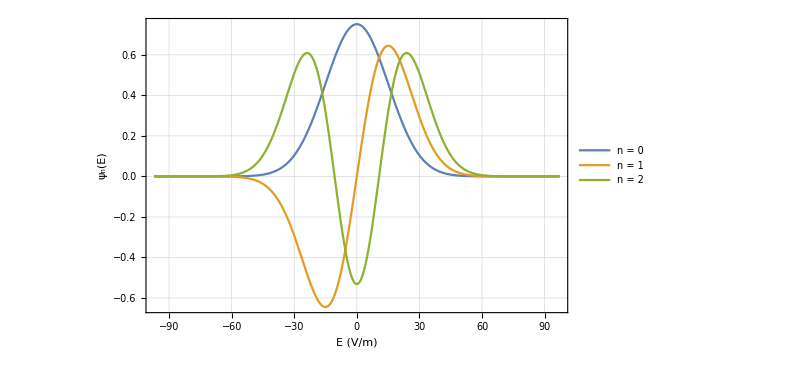

```mathematica
ψVsEPlotData=Table[ψ[n,xE],{n,nMin,nMax}];
Plot[ψVsEPlotData,{Efield,Ex/.{x->xMin},Ex/.{x->xMax}},PlotRange->All,Frame->True,GridLines->Automatic,FrameLabel->{"E (V/m)","ψ_n(E)"},ImageSize->600,FrameStyle->Directive[Black,16],PlotLegends->Placed[Table["n = "<>ToString[n],{n,nMin,nMax}],{0.9,0.85}]]
```